# Modelo versión 3

## Importación de la red:

Pasar a SetDirectory el directorio en donde se encuentra el archivo .graphml para facilidad

Tener en cuenta que i debe cumplir con los valores de num-people

```mathematica
SetDirectory[NotebookDirectory[]];
```

Todas las redes:

```mathematica
ivals={1,2,3,5,10,20};
networksM3=Table[Import[StringJoin["graphs/model-v3/","network-100-",IntegerString[ivals[[i]]],"-1000.graphml"]],{i,1,6,1}];
```

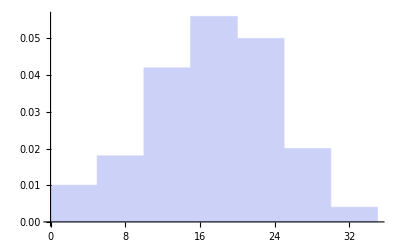
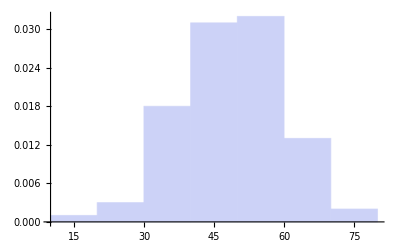
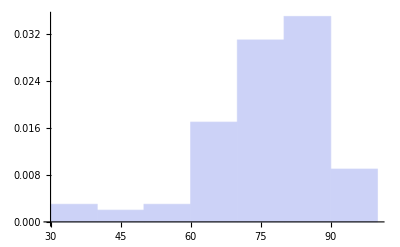
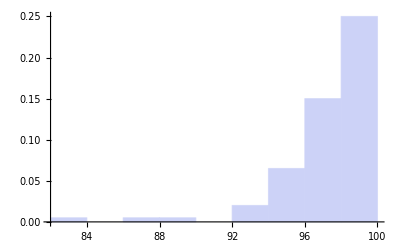
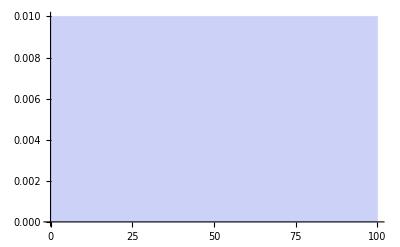
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,6,1}]
```

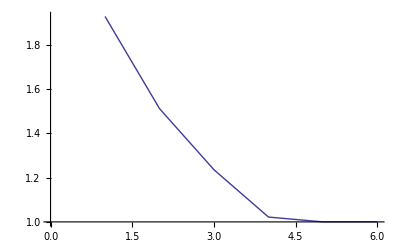

```mathematica
clusteringM3=Map[GlobalClusteringCoefficient,networksM3];
aplM3=Map[MeanGraphDistance,networksM3];
ListPlot[aplM3,Joined->True]
```

```mathematica
ivals={1,2,3,5,10,20};
networksM3=Table[Import[StringJoin["graphs/model-v3/","t10000network-1000-",IntegerString[ivals[[i]]],"-1000.graphml"]],{i,1,6,1}];
```

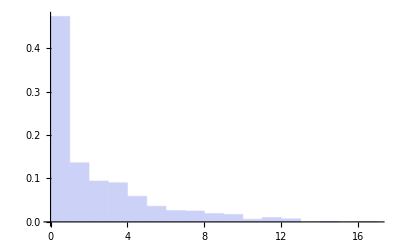
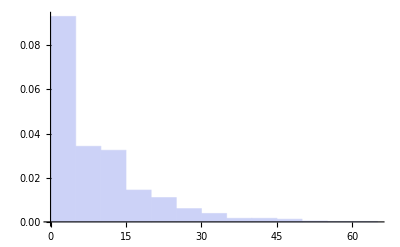
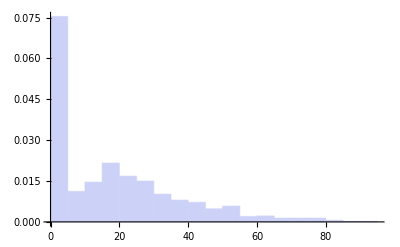
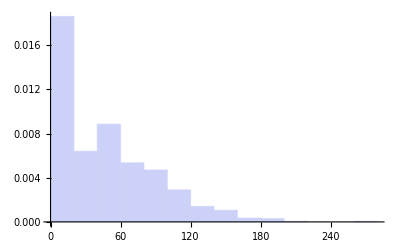
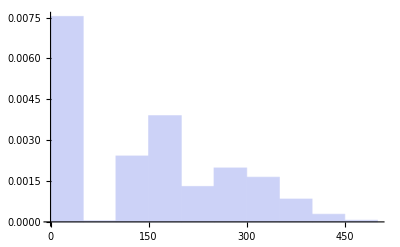
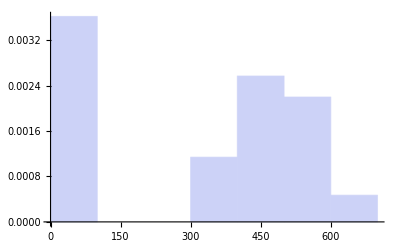

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,6,1}]
```

```mathematica
ivals={1,2,3,5,10,20};
networksM3=Table[Import[StringJoin["graphs/model-v3/p10000/","network-10000-",IntegerString[ivals[[i]]],"-1000.graphml"]],{i,1,2,1}];
```

```mathematica
Table[Histogram[VertexDegree[networksM3[[i]]],Automatic,"PDF"],{i,1,2,1}]
```

Part::partd: Part specification networksM3 ⟦ 1 ⟧ is longer than depth of object.

VertexDegree::graph: A graph object is expected at position 1 in VertexDegree[networksM3 ⟦ 1 ⟧].

Part::partd: Part specification networksM3 ⟦ 1 ⟧ is longer than depth of object.

VertexDegree::graph: A graph object is expected at position 1 in VertexDegree[networksM3 ⟦ 1 ⟧].

Part::partd: Part specification networksM3 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

VertexDegree::graph: A graph object is expected at position 1 in VertexDegree[networksM3 ⟦ 1 ⟧].

General::stop: Further output of VertexDegree :: graph will be suppressed during this calculation.

Histogram::ldata: VertexDegree[networksM3 ⟦ 1 ⟧] is not a valid dataset or list of datasets.

Histogram::ldata: VertexDegree[networksM3 ⟦ 2 ⟧] is not a valid dataset or list of datasets.

Histogram::ldata: VertexDegree[networksM3 ⟦ 1 ⟧] is not a valid dataset or list of datasets.

General::stop: Further output of Histogram :: ldata will be suppressed during this calculation.

{Histogram[VertexDegree[networksM3⟦1⟧],Automatic,PDF],Histogram[VertexDegree[networksM3⟦2⟧],Automatic,PDF]}